# MOT&B-Coils.nb - magnetic fields

Date: 2013-01-08

This Mathematica notebook is written to calculate the magnetic field generated by a pair of coils in anti-Helmholtz configuration for MOT magnetic field gradient and quadrupole trap.  The notebook is modified based on a notebook  from John Thomas’s group at Duke. The notebook is written quite generically, and therefore can be easily adapted to different tasks.

To do the actual “Magnetic Field Calculations”, you must evaluate the “Definitions” section first.  See the “Description” section for help and examples.

Coordinate convention: z (axial), vertical, along gravity; r (radial), horizontal;

Notes: 
1. the same pair of coils is used to generate both MOT magnetic field gradient and quadruple magnetic trap. The magnetic field is switched from MOT configration to B-trap configration by ramping up the current;
2. since the Zeeman coil employs the decreasing field configuration, the radial magnetic field of MOT coils along the Zeeman tube axis is also served as a part of Zeeman slower to deccelate the atomic beam. There will be separate notebooks to calculate the Zeeman field;
3. the MOT/B-trap coils are made of square shaped wires with 1mm × 1mm square outside and with NZ0 layers along radial direction and NR0 layers along axis direction. Two relevant considerations in calculating the magnetic field are:
     b. however, the dimension of the coils is comparable to the distance mentioned above, the accuracy of  the magnetic field calculation is limited by simply counting the turns without considering the change of distance to the center from one turn to the next. Instead, the magnetic field is calculated by adding the field generated by each pair of loops (in anti-Helmholtz con
     figuration). Nevertheless, each loop is regarded as perfectly circular around z-axis without any spiral.

#### Packages

```mathematica
<<NumericalCalculus`
```

### Definitions

#### Universal Constants

```mathematica
Subscript[μ, 0]= 4 π 10^-3;  (* exact,give B-field in Gauss, CODATA 2006 *)
```

#### Calculation Functions

These functions calculate the radial and axial field for a single loop.

```mathematica
Bz[r_,z_,loop_]:=loop[[3]] *(Subscript[μ, 0]/(2 π))/(√((loop[[1]] + r)^2+ (z-loop[[2]])^2)) * (EllipticK[(4 loop[[1]] r)/((loop[[1]]+r)^2+(z-loop[[2]])^2)] + ((loop[[1]]^2 - r^2 - (z-loop[[2]])^2)/((loop[[1]]-r)^2+(z-loop[[2]])^2))*EllipticE[(4 loop[[1]] r)/((loop[[1]]+r)^2+(z-loop[[2]])^2)])
```

```mathematica
Br[r_,z_,loop_]:=loop[[3]]* (z-loop[[2]])*(Subscript[μ, 0] /(2 π r))/(√((loop[[1]] + r)^2+ (z-loop[[2]])^2))* (-EllipticK[(4 loop[[1]] r)/((loop[[1]]+r)^2+(z-loop[[2]])^2)] + ((loop[[1]]^2 + r^2 + (z-loop[[2]])^2)/((loop[[1]]-r)^2+(z-loop[[2]])^2))*EllipticE[(4 loop[[1]] r)/((loop[[1]]+r)^2+(z-loop[[2]])^2)])
```

These functions calculate the field for all of the loops listed in "coil".

```mathematica
AxialField[r_,z_,coil_]:=Module[{},TempFunc[loop_]:=Bz[r,z,loop];
Plus@@Map[TempFunc,coil,{1}]]
```

```mathematica
RadialField[r_,z_,coil_]:=Module[{},TempFunc[loop_]:=Br[r,z,loop];
Plus@@Map[TempFunc,coil,{1}]]
```

This function calculates the field magnitude at any point using the previous functions.

```mathematica
FieldMag[r_,z_,coil_]:=If[r==0,AxialField[r,z,coil],√(AxialField[r,z,coil]^2+RadialField[r,z,coil]^2)]
```

#### Tools for generating "coil" list

```mathematica
Helmholtz[r_,z_,current_]:={{r,-z,current},{r,z,current}}
AntiHelmholtz[r_,z_,current_]:={{r,-z,-current},{r,z,current}}
TrueHelmholtz[z_,current_]:=Helmholtz[2 z,z,current]
TrueAntiHelmholtz[z_,current_]:=AntiHelmholtz[2 z,z,current]
RegularSpacedCoil[InitR_,RStep_, RNum_, InitZ_, ZStep_, ZNum_, Current_]:= Flatten[Table[{InitR+i×RStep, InitZ+j×ZStep,Current}, {i,0,RNum-1},{j,0,ZNum-1}],1]
HelmholtzCoilSet[InitR_,RStep_, RNum_, InitZ_, ZStep_, ZNum_, Current_] :=Flatten[Table[ Helmholtz[InitR+i×RStep, InitZ+j×ZStep,Current], {i,0,RNum-1},{j,0,ZNum-1}],2]
AntiHelmholtzCoilSet[InitR_,RStep_, RNum_, InitZ_, ZStep_, ZNum_, Current_] :=Flatten[Table[ AntiHelmholtz[InitR+i×RStep, InitZ+j×ZStep,Current], {i,0,RNum-1},{j,0,ZNum-1}],2]
```

### Description

#### What this notebook does

This notebook is specific for calculating the magnetic field at any point in space generated by a pair of coils in Helmholtz and anti-Helmholtz configuration.  The calculation shown here accounts for the dimension of the coils, that is, the position difference between loops.  The magnetic field is calculated by adding up the field produced by each pair of loops in anti-Helmholtz (Helmholtz) configuration.

#### How to use this notebook

First, you must make your "coil" list.  This is a list of lists.  You have one internal list for each loop.  Each of these internal loop (singular) lists contains the radius of the loop (in meters), the position of the loop(in meters) along z, and the current (in Amperes).  The following coil list defines one loop with a radius of 10 cm, position of z = 5 cm, and a 1 mA current.

```mathematica
ExampleCoil = {{.1, .05, .01}};
```

Once this is defined, you can determine the axial field (parallel to z), radial field (perpendicular to z), and field magnitude at any point (r, z) with
the functions: AxialField, RadialField, and FieldMag.  each of these functions takes r, z, and your coil list.  All of these functions return the magnetic field in Gauss.  Example:

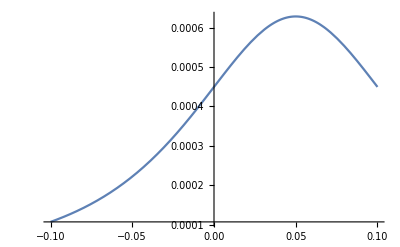

```mathematica
Plot[AxialField[0,z, ExampleCoil], {z, -.1, .1}]
```

#### Generating coils lists

There are several functions to help you generate coils lists.  

The function "Helmholtz" takes  the parameters for a coil list (r, z, current) and returns a coils list with two identical coils.  One has the parameters you specified, and the other has a position of -z.

The function "TrueHelmholtz" takes the same parameters except that it does not take a radius.  The radius is automatically set to 2z.

The functions "AntiHelmholtz" and "TrueAntiHelmholtz" work identically except that the mirror coil has the opposite current.

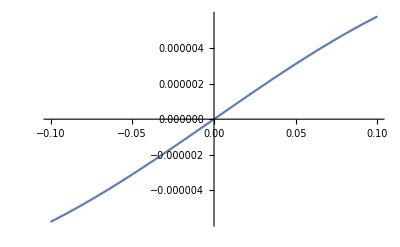

```mathematica
ExampleCoil = AntiHelmholtz[.4, .15,.001];
Plot[AxialField[0,z, ExampleCoil], {z, -.1, .1}]
```

#### Function Summary

coil = {{rad_1,z_1,I_1}, {rad_2,z_2,I_2}, ...}
coil = Helmholtz[rad, z, I]
coil = TrueHelmholtz[z,  I]
coil = AntiHelmholtz[rad, z, I]
coil = TrueAntiHelmholtz[z, I]
coil = HelmholtzCoilSet[r0, dr, Nr, z0, dz, Nz, I]
coil = AntiHelmholtzCoilSet[r0, dr, Nr, z0, dz, Nz, I]

AxialField[r, z, coils]
RadialField[r, z, coils]
FieldMag[r, z, coils]

### Magnetic Field Calculations

#### Experimental values

```mathematica
DR = 0.001;  (* the size of the square wiretube*)
DZ = 0.001; (* the size of the square wire*)
R0= 0.200/2 + 0.001/2;  (* the radius of the first loop in the coil, is given by the CF100 flange size & hollow tube size*)
NR0= 10;  (* the number of turns along radial direction*)
Z0 = 0.2/2 + 0.001/2; (*the position of the first loop along z, is given by the z-direction thickness of the main chamber & hollow tube size *)
NZ0 = 10; (* the number of turns along axial direction*)
Ra = R0 + NR0*DR; (* the initial radius of the 'appended' coil. 'a' here stands for 'appended',this is account for one (or a few) additional out layer(s) which do(es) not have the complete turns as the layers inside.*)
NRa = NR0; (*the number of layers of the 'appended' coil *)
Za = Z0;
NZa =NZ0; (*the number of turns of the 'appended' coil *)
```

#### MOT magnetic field

```mathematica
IMOT = 8; (* the MOT current *)
```

```mathematica
MOTCoil =Join [AntiHelmholtzCoilSet[R0, DR, NR0, Z0, DZ, NZ0, IMOT],AntiHelmholtzCoilSet[Ra, DR, NRa, Za, DZ, NZa, IMOT]]; (*make the MOT coil*)
```

```mathematica
MOTAxialField [z_] := AxialField [0,z, MOTCoil] (*MOT magnetic field along axial direction*)
MOTRadialField[r_] := RadialField [r, 0, MOTCoil] (*MOT magnetic field along radial direction*)
```

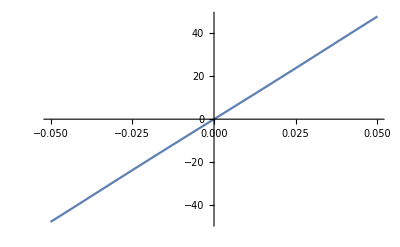

9.61457

```mathematica
Plot[MOTAxialField[z], {z, -0.05, 0.05}] 
MOTAxialGrad = ND [MOTAxialField[z],z,0]/100 (* Gauss/cm, axial magnetic field gradient at the MOT center*)
```

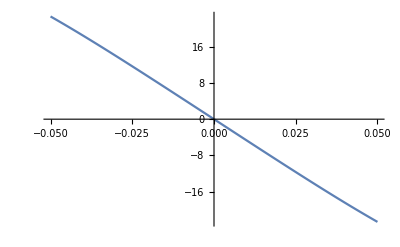

-4.75901

```mathematica
Plot[MOTRadialField[r], {r, -0.05, 0.05}] 
MOTRadialGrad = ND [MOTRadialField[r],r,0.001]/100 (* Gauss/cm, radial magnetic field gradient near the MOT center*)
```

#### B-trap magnetic field

```mathematica
IBtrap = 400 ; (* the B-trap current *)
```

```mathematica
BtrapCoil =Join [AntiHelmholtzCoilSet[R0, DR, NR0, Z0, DZ, NZ0, IBtrap],AntiHelmholtzCoilSet[Ra, DR, NRa, Za, DZ, NZa, IBtrap]]; (*make the Btrap coil*)
```

```mathematica
BtrapAxialField [z_] := AxialField [0,z, BtrapCoil] (*B-trap magnetic field along axial direction*)
BtrapRadialField[r_] := RadialField [r, 0, BtrapCoil] (*B-trap magnetic field along radial direction*)
```

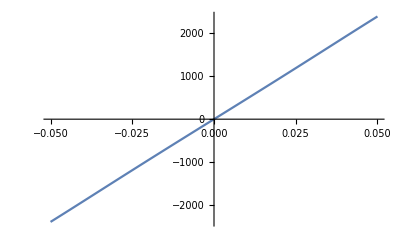

480.729

```mathematica
Plot[BtrapAxialField[z], {z, -0.05, 0.05}] 
BtrapAxialGrad = ND [BtrapAxialField[z],z,0]/100 (* Gauss/cm, axial magnetic field gradient at the B-trap center*)
```

```mathematica
Pi
```

pi

## Resistance

```mathematica
R0=0.0909/2+0.002/2;
rho=0.0175;
L=2*Pi*R0;
S=Pi*R0^2;
R=(rho*L)/S
```

0.753498